# Bistable motif: 2kinase1substrate

## Finding the condition of multistationarity

We consider the following reactions:

K+S→KS→K+S_p
K_p+S→K_p S→K_p+S_p
K→K_p
KS←K_p S
E+S→ES→E+S_p
E_p+S→E_p S→E_p+S_p
E→E_p
ES←E_p S
S_p→S

The species of the system are:

{S,S_p,K,K_p,KS,K_p S,E,E_p,ES,E_p S}

In total, there are 13 reations and 10 species.

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
A=Table[0,{13},{10}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;
A[[2]][[3]]=1;A[[2]][[2]]=1;A[[2]][[5]]=-1;
A[[3]][[1]]=-1;A[[3]][[4]]=-1;A[[3]][[6]]=1;
A[[4]][[4]]=1;A[[4]][[2]]=1;A[[4]][[6]]=-1;
A[[5]][[3]]=-1;A[[5]][[4]]=1;A[[6]][[5]]=1;A[[6]][[6]]=-1;
A[[13]][[2]]=-1;A[[13]][[1]]=1;
A[[7]][[1]]=-1;A[[7]][[7]]=-1;A[[7]][[9]]=1;
A[[8]][[7]]=1;A[[8]][[2]]=1;A[[8]][[9]]=-1;
A[[9]][[1]]=-1;A[[9]][[8]]=-1;A[[9]][[10]]=1;
A[[10]][[8]]=1;A[[10]][[2]]=1;A[[10]][[10]]=-1;
A[[11]][[7]]=-1;A[[11]][[8]]=1;
A[[12]][[9]]=1;A[[12]][[10]]=-1;
```

```mathematica
stoiM=Transpose[A]
```

{{-1,0,-1,0,0,0,-1,0,-1,0,0,0,1},{0,1,0,1,0,0,0,1,0,1,0,0,-1},{-1,1,0,0,-1,0,0,0,0,0,0,0,0},{0,0,-1,1,1,0,0,0,0,0,0,0,0},{1,-1,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,-1,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,-1,0,0},{0,0,0,0,0,0,0,0,-1,1,1,0,0},{0,0,0,0,0,0,1,-1,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,-1,0,-1,0}}

```mathematica
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 4]×Subscript[x, 6],Subscript[k, 5]×Subscript[x, 3],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 7]×Subscript[x, 1],Subscript[k, 8]×Subscript[x, 9],Subscript[k, 9]×Subscript[x, 8]*Subscript[x, 1],Subscript[k, 10]*Subscript[x, 10],Subscript[k, 11]*Subscript[x, 7],Subscript[k, 12]×Subscript[x, 10],Subscript[k, 13]*Subscript[x, 2]}
```

{k_1 x_1 x_3,k_2 x_5,k_3 x_1 x_4,k_4 x_6,k_5 x_3,k_6 x_6,k_7 x_1 x_7,k_8 x_9,k_9 x_1 x_8,k_10 x_10,k_11 x_7,k_12 x_10,k_13 x_2}

```mathematica
ssEqns=stoiM.ks
```

{k_13 x_2-k_1 x_1 x_3-k_3 x_1 x_4-k_7 x_1 x_7-k_9 x_1 x_8,-k_13 x_2+k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10,-k_5 x_3-k_1 x_1 x_3+k_2 x_5,k_5 x_3-k_3 x_1 x_4+k_4 x_6,k_1 x_1 x_3-k_2 x_5+k_6 x_6,k_3 x_1 x_4-k_4 x_6-k_6 x_6,-k_11 x_7-k_7 x_1 x_7+k_8 x_9,k_11 x_7-k_9 x_1 x_8+k_10 x_10,k_7 x_1 x_7-k_8 x_9+k_12 x_10,k_9 x_1 x_8-k_10 x_10-k_12 x_10}

```mathematica
mC=RowReduce[NullSpace[A]]
```

{{1,1,0,0,1,1,0,0,1,1},{0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,1,1}}

```mathematica
cons={Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2],Subscript[x, 7]+Subscript[x, 8]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 3]};
```

```mathematica
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],ssEqns[[8]],ssEqns[[9]],cons[[1]],cons[[2]],cons[[3]]}
```

{-k_13 x_2+k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10,k_5 x_3-k_3 x_1 x_4+k_4 x_6,k_1 x_1 x_3-k_2 x_5+k_6 x_6,k_3 x_1 x_4-k_4 x_6-k_6 x_6,k_11 x_7-k_9 x_1 x_8+k_10 x_10,k_7 x_1 x_7-k_8 x_9+k_12 x_10,-T_1+x_1+x_2+x_5+x_6+x_9+x_10,-T_2+x_3+x_4+x_5+x_6,-T_3+x_7+x_8+x_9+x_10}

```mathematica
sol1=Solve[{ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],cons[[2]]}==0,{Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}]
```

{{x_3→(k_2 k_3 k_6 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_4→(k_2 k_5 (k_4+k_6) T_2)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_5→(k_3 T_2 (k_5 k_6 x_1+k_1 k_6 x_1^2))/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_6→(k_2 k_3 k_5 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)}}

```mathematica
sol2=Solve[{ssEqns[[8]],ssEqns[[9]],ssEqns[[10]],cons[[3]]}==0,{Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[x, 10]}]
```

{{x_7→(k_8 k_9 k_12 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_8→(k_8 k_11 (k_10+k_12) T_3)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_9→(k_9 T_3 (k_11 k_12 x_1+k_7 k_12 x_1^2))/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_10→(k_8 k_9 k_11 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2)}}

```mathematica
sol3=Subscript[x, 2]/.Solve[{ssEqns[[2]]==0},{Subscript[x, 2]}]
```

{(k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10)/k_13}

```mathematica
sol4=Solve[{Subscript[x, 2]==sol3[[1]]}/.Join[sol1[[1]],sol2[[1]]],{Subscript[x, 2]}]
```

{{x_2→1/k_13((k_2 k_3 k_4 k_5 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)+(k_2 k_3 T_2 (k_5 k_6 x_1+k_1 k_6 x_1^2))/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)+(k_8 k_9 k_10 k_11 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2)+(k_8 k_9 T_3 (k_11 k_12 x_1+k_7 k_12 x_1^2))/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2))}}

```mathematica
term=FullSimplify[Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 1]/.Join[sol1[[1]],sol2[[1]],sol4[[1]]]]
```

-T_1+(x_1 ((k_3 T_2 (k_5 (k_6 k_13+k_2 (k_4+k_6+k_13))+k_1 k_6 (k_2+k_13) x_1))/(k_3 k_6 x_1 (k_5+k_1 x_1)+k_2 (k_5 (k_4+k_6)+k_3 (k_5+k_6) x_1))+(k_9 k_12 k_13 (T_3+x_1) (k_11+k_7 x_1)+k_8 (k_11 ((k_10+k_12) k_13+k_9 (k_10+k_12+k_13) T_3)+k_9 ((k_11+k_12) k_13+k_7 k_12 T_3) x_1))/(k_9 k_12 x_1 (k_11+k_7 x_1)+k_8 (k_11 (k_10+k_12)+k_9 (k_11+k_12) x_1))))/k_13

```mathematica
polynomial=Collect[Numerator[Together[term]],Subscript[x, 1]]
```

-k_2 k_4 k_5 k_8 k_10 k_11 k_13 T_1-k_2 k_5 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_8 k_11 k_12 k_13 T_1-k_2 k_5 k_6 k_8 k_11 k_12 k_13 T_1+(k_2 k_4 k_5 k_8 k_10 k_11 k_13+k_2 k_5 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_8 k_11 k_12 k_13+k_2 k_5 k_6 k_8 k_11 k_12 k_13-k_2 k_4 k_5 k_8 k_9 k_11 k_13 T_1-k_2 k_5 k_6 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_5 k_8 k_10 k_11 k_13 T_1-k_2 k_3 k_6 k_8 k_10 k_11 k_13 T_1-k_3 k_5 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_8 k_9 k_12 k_13 T_1-k_2 k_5 k_6 k_8 k_9 k_12 k_13 T_1-k_2 k_3 k_5 k_8 k_11 k_12 k_13 T_1-k_2 k_3 k_6 k_8 k_11 k_12 k_13 T_1-k_3 k_5 k_6 k_8 k_11 k_12 k_13 T_1-k_2 k_4 k_5 k_9 k_11 k_12 k_13 T_1-k_2 k_5 k_6 k_9 k_11 k_12 k_13 T_1+k_2 k_3 k_4 k_5 k_8 k_10 k_11 T_2+k_2 k_3 k_5 k_6 k_8 k_10 k_11 T_2+k_2 k_3 k_4 k_5 k_8 k_11 k_12 T_2+k_2 k_3 k_5 k_6 k_8 k_11 k_12 T_2+k_2 k_3 k_5 k_8 k_10 k_11 k_13 T_2+k_3 k_5 k_6 k_8 k_10 k_11 k_13 T_2+k_2 k_3 k_5 k_8 k_11 k_12 k_13 T_2+k_3 k_5 k_6 k_8 k_11 k_12 k_13 T_2+k_2 k_4 k_5 k_8 k_9 k_10 k_11 T_3+k_2 k_5 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_4 k_5 k_8 k_9 k_11 k_12 T_3+k_2 k_5 k_6 k_8 k_9 k_11 k_12 T_3+k_2 k_4 k_5 k_8 k_9 k_11 k_13 T_3+k_2 k_5 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_4 k_5 k_9 k_11 k_12 k_13 T_3+k_2 k_5 k_6 k_9 k_11 k_12 k_13 T_3) x_1+(k_2 k_4 k_5 k_8 k_9 k_11 k_13+k_2 k_5 k_6 k_8 k_9 k_11 k_13+k_2 k_3 k_5 k_8 k_10 k_11 k_13+k_2 k_3 k_6 k_8 k_10 k_11 k_13+k_3 k_5 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_8 k_9 k_12 k_13+k_2 k_5 k_6 k_8 k_9 k_12 k_13+k_2 k_3 k_5 k_8 k_11 k_12 k_13+k_2 k_3 k_6 k_8 k_11 k_12 k_13+k_3 k_5 k_6 k_8 k_11 k_12 k_13+k_2 k_4 k_5 k_9 k_11 k_12 k_13+k_2 k_5 k_6 k_9 k_11 k_12 k_13-k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_6 k_8 k_9 k_11 k_13 T_1-k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_1-k_1 k_3 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_7 k_9 k_12 k_13 T_1-k_2 k_5 k_6 k_7 k_9 k_12 k_13 T_1-k_2 k_3 k_5 k_8 k_9 k_12 k_13 T_1-k_2 k_3 k_6 k_8 k_9 k_12 k_13 T_1-k_3 k_5 k_6 k_8 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_8 k_11 k_12 k_13 T_1-k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_1-k_2 k_3 k_6 k_9 k_11 k_12 k_13 T_1-k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_1+k_2 k_3 k_4 k_5 k_8 k_9 k_11 T_2+k_2 k_3 k_5 k_6 k_8 k_9 k_11 T_2+k_1 k_2 k_3 k_6 k_8 k_10 k_11 T_2+k_2 k_3 k_4 k_5 k_8 k_9 k_12 T_2+k_2 k_3 k_5 k_6 k_8 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_8 k_11 k_12 T_2+k_2 k_3 k_4 k_5 k_9 k_11 k_12 T_2+k_2 k_3 k_5 k_6 k_9 k_11 k_12 T_2+k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_2+k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_2+k_1 k_3 k_6 k_8 k_10 k_11 k_13 T_2+k_2 k_3 k_5 k_8 k_9 k_12 k_13 T_2+k_3 k_5 k_6 k_8 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_11 k_12 k_13 T_2+k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_2+k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_2+k_2 k_3 k_5 k_8 k_9 k_10 k_11 T_3+k_2 k_3 k_6 k_8 k_9 k_10 k_11 T_3+k_3 k_5 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_4 k_5 k_7 k_8 k_9 k_12 T_3+k_2 k_5 k_6 k_7 k_8 k_9 k_12 T_3+k_2 k_3 k_5 k_8 k_9 k_11 k_12 T_3+k_2 k_3 k_6 k_8 k_9 k_11 k_12 T_3+k_3 k_5 k_6 k_8 k_9 k_11 k_12 T_3+k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_3+k_2 k_3 k_6 k_8 k_9 k_11 k_13 T_3+k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_4 k_5 k_7 k_9 k_12 k_13 T_3+k_2 k_5 k_6 k_7 k_9 k_12 k_13 T_3+k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_3+k_2 k_3 k_6 k_9 k_11 k_12 k_13 T_3+k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_3) x_1^2+(k_2 k_3 k_5 k_8 k_9 k_11 k_13+k_2 k_3 k_6 k_8 k_9 k_11 k_13+k_3 k_5 k_6 k_8 k_9 k_11 k_13+k_1 k_3 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_7 k_9 k_12 k_13+k_2 k_5 k_6 k_7 k_9 k_12 k_13+k_2 k_3 k_5 k_8 k_9 k_12 k_13+k_2 k_3 k_6 k_8 k_9 k_12 k_13+k_3 k_5 k_6 k_8 k_9 k_12 k_13+k_1 k_3 k_6 k_8 k_11 k_12 k_13+k_2 k_3 k_5 k_9 k_11 k_12 k_13+k_2 k_3 k_6 k_9 k_11 k_12 k_13+k_3 k_5 k_6 k_9 k_11 k_12 k_13-k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_1-k_2 k_3 k_6 k_7 k_9 k_12 k_13 T_1-k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_8 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_1+k_1 k_2 k_3 k_6 k_8 k_9 k_11 T_2+k_2 k_3 k_4 k_5 k_7 k_9 k_12 T_2+k_2 k_3 k_5 k_6 k_7 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_8 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_9 k_11 k_12 T_2+k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_2+k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_2+k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_3 k_5 k_7 k_8 k_9 k_12 T_3+k_2 k_3 k_6 k_7 k_8 k_9 k_12 T_3+k_3 k_5 k_6 k_7 k_8 k_9 k_12 T_3+k_1 k_3 k_6 k_8 k_9 k_11 k_12 T_3+k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_3+k_2 k_3 k_6 k_7 k_9 k_12 k_13 T_3+k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_3+k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_3) x_1^3+(k_1 k_3 k_6 k_8 k_9 k_11 k_13+k_2 k_3 k_5 k_7 k_9 k_12 k_13+k_2 k_3 k_6 k_7 k_9 k_12 k_13+k_3 k_5 k_6 k_7 k_9 k_12 k_13+k_1 k_3 k_6 k_8 k_9 k_12 k_13+k_1 k_3 k_6 k_9 k_11 k_12 k_13-k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_1+k_1 k_2 k_3 k_6 k_7 k_9 k_12 T_2+k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_7 k_8 k_9 k_12 T_3+k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_3) x_1^4+k_1 k_3 k_6 k_7 k_9 k_12 k_13 x_1^5

This is a degree 5 polynomial which presumably admits 5 positive real roots. Any real root of this polynomial leads to a steady state for the fixed rate constants and total amounts. The values of the other variables at steady states are found by plugging the value of x1 (the root of the polynomial) into the expressions in sol1, sol2, and sol3 above.

A necessary condition for 5 positive roots is that the signs of the coefficient of the polynomial (in x1) alternate.
This is a pre-check when you do the sampling: you need to impose the coefficient of x1^4 to be  negative , the coefficient of x1^3 to be positive, the coefficient of x1^2 to be  negative and the coefficient of x1 to be positive. The coefficients of x1^5 and the independent term always have the right sign.

## Sampling the parameters to make the term has 5 roots

```mathematica
ClearAll["Global`*"];
pol=-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^2+(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^3+(Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^4+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[x, 1]^5;
```

#### Coeffs

```mathematica
coeff1=Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3];
coeff2=(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
coeff3=(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
coeff4=(Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
```

#### Sampling

```mathematica
ss2ParSets={};
ss2PolSets={};
ss2SolSets={};
ss3ParSets={};
ss3PolSets={};
ss3SolSets={};
ss4ParSets={};
ss4PolSets={};
ss4SolSets={};
ss5ParSets={};
ss5PolSets={};
ss5SolSets={};
biCount=0;
multiCount=0;
termCount=0;
Timing[
Do[{
(*pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],13]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],3]]*1000;*)
pars=Exp[RandomReal[{Log[0.001],Log[1000.]},13]];
tots=Exp[RandomReal[{Log[0.001],Log[1000.]},3]];
subs={Subscript[k, 1]->pars[[1]],Subscript[k, 2]->pars[[2]],Subscript[k, 3]->pars[[3]],Subscript[k, 4]->pars[[4]],Subscript[k, 5]->pars[[5]],Subscript[k, 6]->pars[[6]],Subscript[k, 7]->pars[[7]],Subscript[k, 8]->pars[[8]],Subscript[k, 9]->pars[[9]],Subscript[k, 10]->pars[[10]],Subscript[k, 11]->pars[[11]],Subscript[k, 12]->pars[[12]],Subscript[k, 13]->pars[[13]],Subscript[T, 1]->tots[[1]],Subscript[T, 2]->tots[[2]],Subscript[T, 3]->tots[[3]]};
(*term4=coeff4/.subs;term3=coeff3/.subs;term2=coeff2/.subs;term1=coeff1/.subs;
If[term4<0&&term3>0&&term2<0&&term1>0,{*)
solution=Select[DeleteDuplicates[Re[Subscript[x, 1]/.NSolve[{pol==0}/.subs,Subscript[x, 1]]]],Positive];
(*termCount++;*)
Switch[Length[Flatten[solution]],2,{
AppendTo[ss2ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss2PolSets,pol/.subs];
AppendTo[ss2SolSets,Flatten[solution]];
biCount++;},3,{
AppendTo[ss3ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss3PolSets,pol/.subs];
AppendTo[ss3SolSets,Flatten[solution]];
multiCount++;},4,{
AppendTo[ss4ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss4PolSets,pol/.subs];
AppendTo[ss4SolSets,Flatten[solution]];
multiCount++;},5,{
AppendTo[ss5ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss5PolSets,pol/.subs];
AppendTo[ss5SolSets,Flatten[solution]];
multiCount++;}
];
(*}];*)
},{i,5000000}];
]
```

{15675.3,Null}

#### Check results

```mathematica
Length[ss2ParSets]
```

40267

```mathematica
Length[ss3ParSets]
```

6513

```mathematica
Length[ss4ParSets]
```

135

```mathematica
Length[ss5ParSets]
```

4

#### Save all sampling data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["2kinase_ss5ParSets.csv",ss5ParSets];
```

```mathematica
Export["2kinase_ss5SolSets.csv",ss5SolSets];
```

```mathematica
Export["2kinase_ss5PolSets.csv",ss5PolSets];
```

```mathematica
Export["2kinase_ss4ParSets.csv",ss4ParSets];
Export["2kinase_ss4SolSets.csv",ss4SolSets];
Export["2kinase_ss4PolSets.csv",ss4PolSets];

Export["2kinase_ss3ParSets.csv",ss3ParSets];
Export["2kinase_ss3SolSets.csv",ss3SolSets];
Export["2kinase_ss3PolSets.csv",ss3PolSets];

Export["2kinase_ss2ParSets.csv",ss2ParSets];
Export["2kinase_ss2SolSets.csv",ss2SolSets];
Export["2kinase_ss2PolSets.csv",ss2PolSets];
```

### SS5

#### Show the parameters

```mathematica
InputForm[ss5ParSets]
```

{{30.26907055950005, 0.015345031904046718, 379.2818135708148, 3.8082251354658188, 0.0036687528444848427, 
 0.13296589686376084, 310.1595399836181, 0.021043418057000815, 0.016491372377285016, 39.76104156980563, 9.061356696657525, 
 0.023576257909081366, 0.0023689836151906487, 845.7868156657265, 57.56286728182886, 16.45292963069698}, {12.791536262377333, 
 0.0034898324955981988, 124.48490665956912, 14.364956625123318, 1.8820643829200225, 0.06207039508084975, 5.36634369662495, 
 0.1395233965784267, 6.127307127467282, 348.2943196285812, 0.6139560154556575, 0.004203521315153397, 0.006595294405600259, 
 431.8992457693107, 12.136890753339557, 0.18502617556413403}, {5.879137085516735, 0.0033751979024755916, 2.107719796978838, 
 500.69023689470674, 0.037972916416413455, 48.025982227857675, 67.40947817881231, 0.004277486460006026, 0.16410793866624665, 
 30.195763275878235, 0.4278526927277934, 0.002727157259805876, 0.0015127395140503617, 829.7331212580159, 110.97744997193716, 
 25.07248294701992}, {0.03863067640002412, 0.06964020400731227, 12.893107874913023, 717.0141199745967, 0.016845994678178475, 
 0.001941863314613148, 0.515261967967496, 0.0011924697492939357, 58.62046075778042, 242.79254583735883, 
 0.0018562783780476306, 4.143110610314261, 0.0034828788856501665, 980.5678137212656, 0.02294111016031769, 
 200.56979547299036}}

```mathematica
InputForm[ss5SolSets]
```

{{0.0001673179574018385, 0.0017701734788143613, 4.211495208850604, 28.136233827022362, 220.35377804688864}, 
 {0.0026993292596905116, 0.5143459784462802, 1.8447433928056391, 126.15341072811653, 276.6322493206081}, 
 {0.011201423386435755, 0.024705675213822165, 0.13170436103981822, 13.63860745022466, 361.34661097799966}, 
 {0.00045859801424694336, 0.013160505343201727, 11.37445257762346, 92.04118330552284, 589.5323347053119}}

```mathematica
ss5SolSets
```

{{0.000167318,0.00177017,4.2115,28.1362,220.354},{0.00269933,0.514346,1.84474,126.153,276.632},{0.0112014,0.0247057,0.131704,13.6386,361.347},{0.000458598,0.0131605,11.3745,92.0412,589.532}}

```mathematica
InputForm[ss5ParSets[[3]]]
```

{5.879137085516735, 0.0033751979024755916, 2.107719796978838, 500.69023689470674, 0.037972916416413455, 
48.025982227857675, 67.40947817881231, 0.004277486460006026, 0.16410793866624665, 30.195763275878235, 
0.4278526927277934, 0.002727157259805876, 0.0015127395140503617, 829.7331212580159, 110.97744997193716, 
25.07248294701992}

#### Get the parameters

```mathematica
ss5Par3={5.879137085516735,0.0033751979024755916,2.107719796978838,500.69023689470674,0.037972916416413455,48.025982227857675,67.40947817881231,0.004277486460006026,0.16410793866624665,30.195763275878235,0.4278526927277934,0.002727157259805876,0.0015127395140503617,829.7331212580159,110.97744997193716,25.07248294701992}
```

{5.87914,0.0033752,2.10772,500.69,0.0379729,48.026,67.4095,0.00427749,0.164108,30.1958,0.427853,0.00272716,0.00151274,829.733,110.977,25.0725}

```mathematica
parSet={Subscript[k, 1]->ss5Par3[[1]],Subscript[k, 2]->ss5Par3[[2]],Subscript[k, 3]->ss5Par3[[3]],Subscript[k, 4]->ss5Par3[[4]],Subscript[k, 5]->ss5Par3[[5]],Subscript[k, 6]->ss5Par3[[6]],Subscript[k, 7]->ss5Par3[[7]],Subscript[k, 8]->ss5Par3[[8]],Subscript[k, 9]->ss5Par3[[9]],Subscript[k, 10]->ss5Par3[[10]],Subscript[k, 11]->ss5Par3[[11]],Subscript[k, 12]->ss5Par3[[12]],Subscript[k, 13]->ss5Par3[[13]],Subscript[T, 1]->ss5Par3[[14]](*,Subscript[T, 2]->ss5Par3[[15]],Subscript[T, 3]->ss5Par3[[16]]*)};
```

```mathematica
polx1=pol==0/.parSet
```

-0.00487856+(-0.290402+0.00851361 T_2+0.000637903 T_3) x_1+(-41.2881+0.160843 T_2+0.0379793 T_3) x_1^2+(-0.477551+0.0060836 T_2+5.39877 T_3) x_1^3+(-22.5348+0.0877585 T_2+0.103958 T_3) x_1^4+0.0271599 x_1^5==0

#### ParSet[[3]]: Varying T_2

```mathematica
oneDT2=Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->T2,Subscript[T, 3]->25.07248294701992},{Subscript[x, 1]}],{T2,0,300,1}];
```

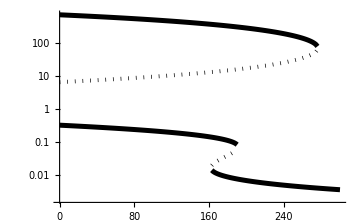

```mathematica
ListLogPlot[(*Join[{Range[0,200,0.1]},*)Transpose[oneDT2[[1;;200]]](*]*),Joined->True,ImageSize->Medium,DataRange->{0,300},PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]}},(*PlotRange->{{0,200},{0.001,1000}},*)LabelStyle->{14,GrayLevel[0]}]
```

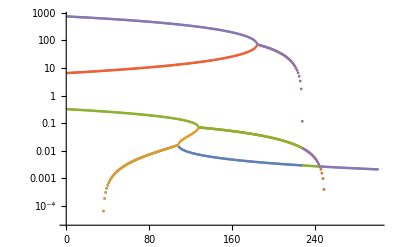

```mathematica
ListLogPlot[Transpose[Re[oneDT2]]]
```

#### ParSet[[3]]: Varying T_3

```mathematica
oneDT3=Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->110.97744997193716,Subscript[T, 3]->T3(*25.07248294701992*)},{Subscript[x, 1]}],{T3,0,80,0.1}];
```

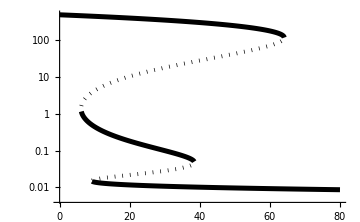

```mathematica
ListLogPlot[(*Join[{Range[0,200,0.1]},*)Transpose[oneDT3(*[[1;;100]]*)](*]*),DataRange->{0,80},Joined->True,ImageSize->Medium,PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]}},(*PlotRange->{{0,200},{0.001,1000}},*)LabelStyle->{14,GrayLevel[0]}]
```

#### ParSet[[3]]: Varying both T_2 and T_3

```mathematica
twoD=Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->T2(*110.97744997193716*),Subscript[T, 3]->T3(*25.07248294701992*)},{Subscript[x, 1]}],{T2,0,280,2.8},{T3,0,160,1.6}];
```

```mathematica
normal3D=ListPointPlot3D[Log10[Transpose[twoD,{2,3,1}]],DataRange->{{0,280},{0,160}},PlotStyle->PointSize[Medium],ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ViewPoint->{-1.9678567233048574,-2.120404270561833,-1.7553989990674568},ViewVertical->{-0.06442955334612624,-0.058712697461734124,-2.4904839537381904}]
```

-Graphics3D-

```mathematica
optsNormal3D=-Graphics3D-//Options
```

{Axes→True,AxesLabel→{None,None,None},BoxRatios→{1,1,0.4},FaceGridsStyle→Automatic,ImageSize→{396.9,288.539},LabelStyle→{18,GrayLevel[0]},PlotRange→{{0.,280.},{0.,160.},Automatic},PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]},{Automatic,Automatic}},Ticks→{Automatic,Automatic,Automatic},ViewPoint→{-1.96786,-2.1204,-1.7554},ViewVertical→{-0.0644296,-0.0587127,-2.49048}}

```mathematica
Rasterize[ListPointPlot3D[coords,ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]},PlotStyle->PointSize[Medium],PlotLegends->Automatic,ViewPoint->{-1.9678567233048574,-2.120404270561833,-1.7553989990674568},ViewVertical->{-0.06442955334612624,-0.058712697461734124,-2.4904839537381904},ImageSize->Large]]
```

-Graphics-

ContourPlot3D:

```mathematica
logTransTwoD=Log10[Transpose[twoD,{2,3,1}]];dim=Dimensions[logTransTwoD];t2=Range[0,280,2.8];t3=Range[0,160,1.6];
```

```mathematica
nestedCoords=Table[{t2[[k]],t3[[j]],logTransTwoD[[i]][[j]][[k]]},{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];
```

```mathematica
coords=Table[Flatten[nestedCoords[[i]],1],{i,1,Length[nestedCoords]}];
```

```mathematica
(*Cannot use contour plot, shame*)
small3D=ListPointPlot3D[coords,ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]}(*,PlotStyle->PointSize[Small]*),ImageSize->Large]
```

-Graphics3D-

```mathematica
optsSmall3D=-Graphics3D-//Options
```

{Axes→True,AxesLabel→{None,None,None},BoxRatios→{1,1,0.4},FaceGridsStyle→Automatic,ImageSize→{362.874,307.339},LabelStyle→{18,GrayLevel[0]},PlotRange→{{0.,280.},{0.,160.},Automatic},PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]},{Automatic,Automatic}},Ticks→{Automatic,Automatic,Automatic},ViewPoint→{1.69265,1.82147,2.29504},ViewVertical→{-0.0963563,-0.0639817,2.48322}}

```mathematica
Rasterize[ListPointPlot3D[coords,ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]}(*,PlotStyle->PointSize[Small]*),PlotLegends->Automatic,ViewPoint->{10, 10, 10},ImageSize->Large]]
```

-Graphics-